### Model: Cylinder of radius a and length L_0.

```mathematica
a=20;L0=80;
```

```mathematica
(*Calculating the theoretical curve from a cylinder of radius a and height L0*)
```

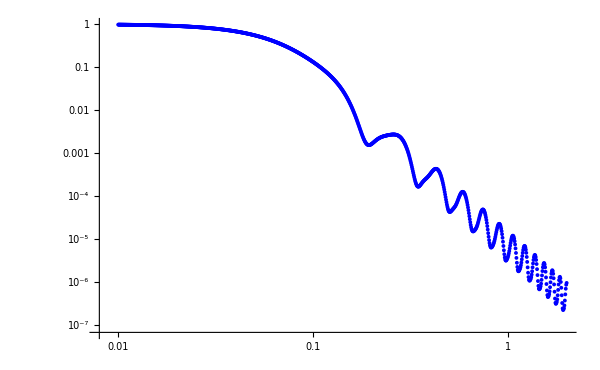

```mathematica
CylinderFF[q0_]:= Module[{q=q0,R0=20,L0=80,fun,F,res},
F[q_,μ_]:=Sin[q μ L0/2]/(q μ L0/2)(2 BesselJ[1,q √(1-μ^2) R0])/(q √(1-μ^2) R0);
res=1/2 NIntegrate[Evaluate[F[q,μ]^2],{μ,-1,1} ];res];
equalLogq[qmin_,qmax_,n_]:=Range[Log[qmin],Log[qmax],(Log[qmax]-Log[qmin])/n];
datacylinder= Table[{ⅇ^q,CylinderFF[ⅇ^q]},{q,equalLogq[.01,2,1000]}]//N;
theorplotcylinder=ListLogLogPlot[datacylinder,PlotStyle->{Thick,Blue},ImageSize->600]
```

```mathematica
Export["SAS_theor_cylinder.dat",datacylinder]
```

SAS_theor_cylinder.dat

```mathematica
(*===========================================================================*)
```

```mathematica
(*Calculating the numerical curve from the same cylinder, by using Monte Carlo simulations*)
```

```mathematica
SeedRandom[12345];
reg=DiscretizeRegion[Cylinder[{{0,0,0},{0,0,L0}},a]];
k=Ceiling[55 10^-2 RegionMeasure[reg]];
bounds=RegionBounds[reg];
pts=RandomVariate[UniformDistribution[bounds],k];
col=RegionMember[reg,pts]/.{False->Gray,True->Blue};
cylinderpts=Select[pts,RegionMember[reg]];
discretecylinder=Graphics3D[{AbsolutePointSize[2],Blue,Point[cylinderpts]},Boxed->False];
```

```mathematica
(*Visual check wheather the generated distribution of points lies inside the theoretical model*)
```

```mathematica
continuouscylinder=Graphics3D[{EdgeForm[Directive[Thickness[0.01],Black]],FaceForm[{Black,Opacity[0.03]}],Cylinder[{{0,0,0},{0,0,L0}},a]},Boxed->False];
Show[continuouscylinder,discretecylinder]
```

-Graphics3D-

```mathematica
(*Calculating the pddf*)
```

```mathematica
Length[cylinderpts]
```

43171

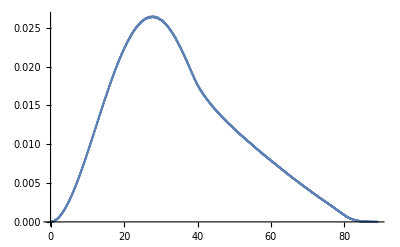

```mathematica
eds=EuclideanDistance@@@Subsets[cylinderpts,{2}];
data=HistogramList[eds,{100 Min[eds]/Max[eds]}];
bins=Max[eds]/Length[data[[2]]] Table[i,{i,1,Length[data[[2]]]}];
datapart=Partition[Riffle[bins,data[[2]]],2]//N;
area=Differences[#1].MovingAverage[#2,2]&@@Transpose[datapart];
datapartnew2=Partition[Riffle[bins,data[[2]]/area],2]//N;
plotdatapart=ListPlot[{datapartnew2}]
```

```mathematica
Export["pddf_MC_simulations_cylinder.dat",datapartnew2]
```

pddf_MC_simulations_cylinder.dat

```mathematica
(*the Fourier transform of pddf*)
```

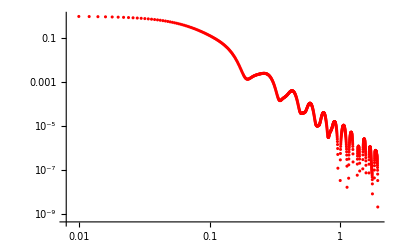

```mathematica
q=Table[i,{i,0.01,2,.002}];Pq=List[#,1/2 Total[Differences[Partition[Riffle[bins,datapartnew2[[All,2]] Sin[# bins]/(# bins)],2][[All,1]]] ListCorrelate[{1,1},Partition[Riffle[bins,datapartnew2[[All,2]] Sin[# bins]/(# bins)],2][[All,2]]]]]&/@q;
mcplot=ListLogLogPlot[{Pq},PlotStyle->{Red,Blue,Green,Black},Joined->False,PlotRange->All]
```

```mathematica
Export["SAS_MC_simulations-cylinder.dat",Pq]
```

SAS_MC_simulations-cylinder.dat